```mathematica
f[x_,n_]:=Piecewise[{{{{0}, {n x}}, {{x≤0}, {0<x<1/n}}}, {1, x≥1/n}}]
```

```mathematica
Plot[f[x,5],{x,-1,1}]
```

LogicalExpand::elist: List encountered during logical expansion of {{-0.999959}, {False}}.

LogicalExpand::elist: List encountered during logical expansion of {{-0.959143}, {False}}.

LogicalExpand::elist: List encountered during logical expansion of {{-0.918326}, {False}}.

General::stop: Further output of LogicalExpand :: elist will be suppressed during this calculation.

Plot::exclul: {Max[1/5 - x, ! {{x}, {0 < x < 1/5}}] - 0, LogicalExpand[{{x}, {0 < x < 1/5}}] - 0, Max[-1/5 + x, ! {{x}, {0 < x < 1/5}}] - 0} must be a list of equalities or real-valued functions.

-Graphics-

```mathematica
?Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i.

```mathematica
?Condition
```

patt/;test is a pattern which matches only if the evaluation of test yields True. 
lhs:>rhs/;test represents a rule which applies only if the evaluation of test yields True. 
lhs:=rhs/;test is a definition to be used only if test yields True.

```mathematica
g[x_,n_]:=0 /;x≤0
```

```mathematica
g[x_,n_]:=n x/;0<x<1/n
```

```mathematica
g[x_,n_]:=1/;x≥1/n
```

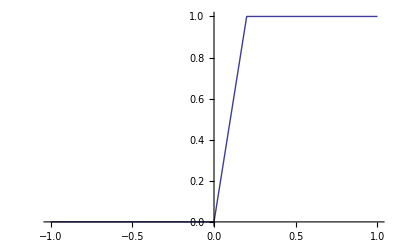

```mathematica
Plot[g[x,5],{x,-1,1}]
```

```mathematica
h
```

```mathematica
h[x_]:=Piecewise[{{{{0}, {5x}}, {{x≤0}, {0<x<1/5}}}, {1, x≥1/5}}]
```

```mathematica
Plot[h[x],{x,-1,1}]
```

LogicalExpand::elist: List encountered during logical expansion of {{-0.999959}, {False}}.

LogicalExpand::elist: List encountered during logical expansion of {{-0.959143}, {False}}.

LogicalExpand::elist: List encountered during logical expansion of {{-0.918326}, {False}}.

General::stop: Further output of LogicalExpand :: elist will be suppressed during this calculation.

Plot::exclul: {Max[1/5 - x, ! {{x}, {0 < x < 1/5}}] - 0, LogicalExpand[{{x}, {0 < x < 1/5}}] - 0, Max[-1/5 + x, ! {{x}, {0 < x < 1/5}}] - 0} must be a list of equalities or real-valued functions.

-Graphics-

```mathematica
k[x_,n_Integer]:=0/;x≤0;
k[x_,n_Integer]:=n*x/;0<x<1/n;
k[x_,n_Integer]:=1/;x≥1/n;
```

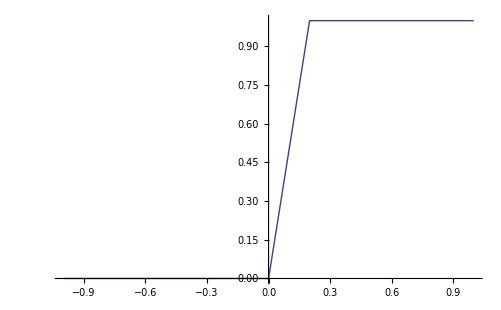

```mathematica
Plot[k[x,5],{x,-1,1}]
```

```mathematica
Plot[k[x,n],{{x,-1,1},{n,1,5}}]
```

Plot::pllim: Range specification {{x, -1, 1}, {n, 1, 5}} is not of the form {x, xmin, xmax}.

```mathematica
Plot[k[x,n],{x,-1,1},{n,1,5}]
```

Plot::nonopt: Options expected (instead of {n, 1, 5}) beyond position 2 in Plot[k[x, n], {x, -1, 1}, {n, 1, 5}]. An option must be a rule or a list of rules.

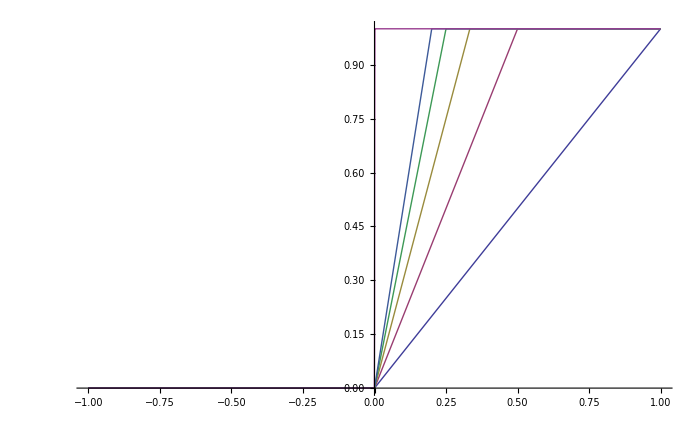

```mathematica
Plot[{k[x,1],k[x,2],k[x,3],k[x,4],k[x,5],k[x,1000]},{x,-1,1}]
```

```mathematica
?Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i.

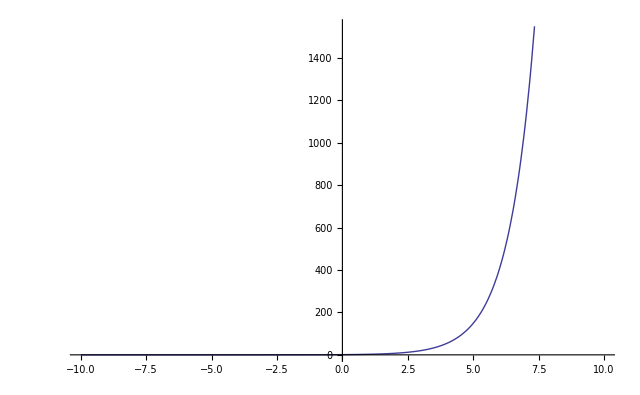

```mathematica
Plot[Exp[x],{x,-10,10}]
```

```mathematica
Log[Exp[5]]
```

5

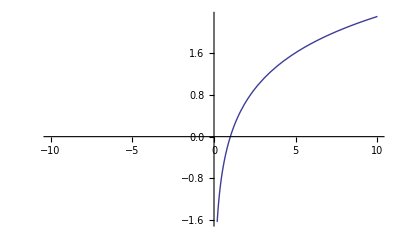

```mathematica
Plot[Log[x],{x,-10,10}]
```

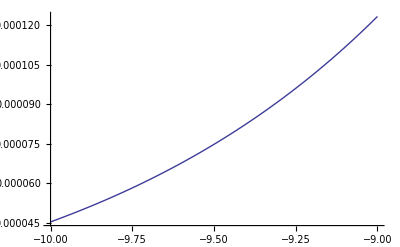

```mathematica
Plot[Exp[x],{x,-10,-9}]
```

```mathematica
h[x_]:=-x/;x≤0;
h[x_]:=1-Exp[x]/;x>0;
```

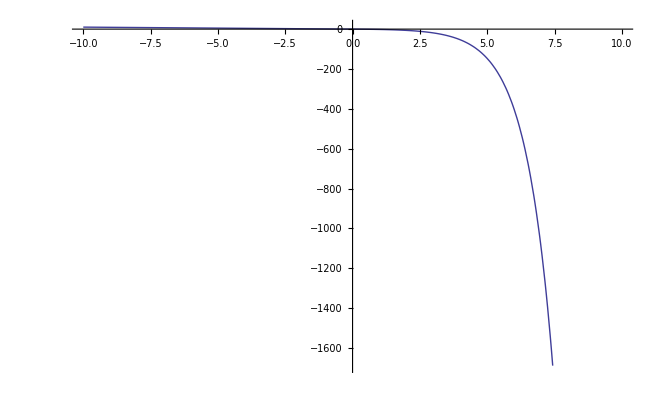

```mathematica
Plot[h[x],{x,-10,10}]
```

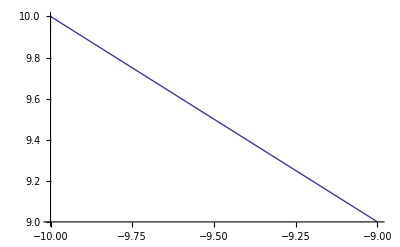

```mathematica
Plot[h[x],{x,-10,-9}]
```

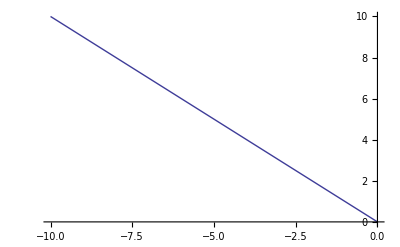

```mathematica
Plot[h[x],{x,-10,0}]
```

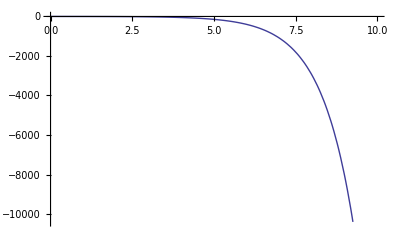

```mathematica
Plot[h[x],{x,0,10}]
```

```mathematica
Limit[1-Exp[x],x->Infinity]
```

-∞

```mathematica
h[5]
```

1-ⅇ^5

```mathematica
%/NN
```

(1-ⅇ^5)/NN

```mathematica
%//N
```

```mathematica
h[5]
```

1-ⅇ^5

```mathematica
%//N
```

-147.413

```mathematica
h[-5]
```

5

```mathematica
h[10]
```

1-ⅇ^10

```mathematica
%//N
```

-22025.5

```mathematica
26^k*26^k
```

26^(2 k)